```mathematica
NotebookEvaluate[FileNameJoin[{NotebookDirectory[],"../../mathematica_utilities/mathematica_plot_options.nb"}]];
plot2Doption=Append[{PlotRange->All,PlotStyle->Red,Filling->Axis,GridLines->All,Joined->False},plot2Doption];
```

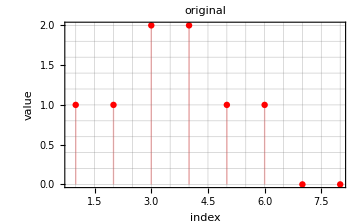

/Users/tomoaki/Library/CloudStorage/Dropbox/code/cpp/builds/build_Fourier/./sample_original_mathematica.png

```mathematica
casename="cosWave";

(*cosWave*)
If[casename=="mathematica",
list={1.,1.,2.,2.,1.,1.,0.,0.};
]

n=20;
(*cosWave*)
If[casename=="cosWave",
list=Table[Cos[2π/n*i],{i,0,n-1,1}];
]

(*squareWave*)
If[casename=="squareWave",
list=Flatten[Table[{Table[-1,{i,1,n/2,1}],Table[1,{i,1,n/2,1}]},{i,1,2}]];
]

(*triangleWave*)
If[casename=="triangleWave",
halfWave=Join[Table[i,{i,-1,1,2/(n-1)}],Table[i,{i,1,-1,-2/(n-1)}][[2;;-2]]];
list=Flatten[{halfWave,halfWave}];
]

(*list=Table[Cos[2π/n*i]*Cos[5π/n*i],{i,0,n-1,1}];*)
fig=ListPlot[list,PlotLabel->"original",FrameLabel->{"index","value"},GridLines->All, Joined->False,Evaluate[plot2Doption]]
Export[FileNameJoin[{NotebookDirectory[],"./sample_original_"<>casename<>".png"}],fig]
```

```mathematica
num=30
(*list=Flatten@{Table[1,{i,1,num}],Table[2,{i,1,num}]}*)
(*list=Table[Cos[2π*i/num],{i,0,num-1}]*)
MyFourier[list_,n_]:=With[{len=Length[list]},Sum[list[[k+1]]*Exp[-I*n*2. π/len*k],{k,0,len-1}]/len];
Column[Fourier[list,FourierParameters->{-1,-1}],Frame->All]
Column[cn=Table[MyFourier[list,n],{n,0,Length[list]-1}],Frame->All]
```

30

1.+0. ⅈ
-0.176777-0.426777 ⅈ
0.+0. ⅈ
0.176777+0.0732233 ⅈ
0.+0. ⅈ
0.176777-0.0732233 ⅈ
0.+0. ⅈ
-0.176777+0.426777 ⅈ

1.
-0.176777-0.426777 ⅈ
-1.72409×10^-17+0. ⅈ
0.176777+0.0732233 ⅈ
0.-6.12323×10^-17 ⅈ
0.176777-0.0732233 ⅈ
-2.25833×10^-16-2.77556×10^-17 ⅈ
-0.176777+0.426777 ⅈ

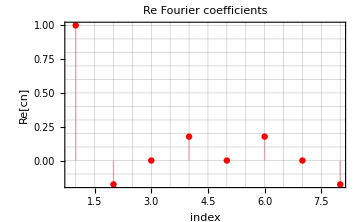

/Users/tomoaki/Library/CloudStorage/Dropbox/code/cpp/builds/build_Fourier/./sample_Re_cn_mathematica.png

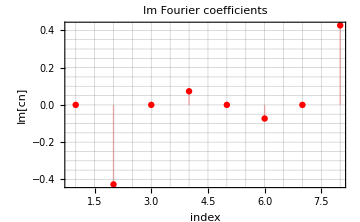

/Users/tomoaki/Library/CloudStorage/Dropbox/code/cpp/builds/build_Fourier/./sample_Im_cn_mathematica.png

/Users/tomoaki/Library/CloudStorage/Dropbox/code/cpp/builds/build_Fourier/./sample_ReIm_cn_mathematica.png

```mathematica
figRe=ListPlot[Re[cn],PlotLabel->"Re Fourier coefficients",FrameLabel->{"index","Re[cn]"},Evaluate[plot2Doption]]
Export[FileNameJoin[{NotebookDirectory[],"./sample_Re_cn_"<>casename<>".png"}],figRe]

figIm=ListPlot[Im[cn],PlotLabel->"Im Fourier coefficients",FrameLabel->{"index","Im[cn]"},Evaluate[plot2Doption]]
Export[FileNameJoin[{NotebookDirectory[],"./sample_Im_cn_"<>casename<>".png"}],figIm]

Export[FileNameJoin[{NotebookDirectory[],"./sample_ReIm_cn_"<>casename<>".png"}],Row[{figRe,figIm}]]
```

1.+2.20344×10^-17 ⅈ
1.-6.32426×10^-17 ⅈ
2.-1.44499×10^-16 ⅈ
2.+1.85707×10^-16 ⅈ
1.-2.0001×10^-16 ⅈ
1.+6.02891×10^-16 ⅈ
3.33067×10^-16+7.75455×10^-17 ⅈ
2.22045×10^-16-4.80427×10^-16 ⅈ

1.+0. ⅈ
1.+0. ⅈ
2.-1.38778×10^-16 ⅈ
2.+1.11022×10^-16 ⅈ
1.-2.22045×10^-16 ⅈ
1.+6.10623×10^-16 ⅈ
2.77556×10^-16+8.32667×10^-17 ⅈ
4.996×10^-16-4.996×10^-16 ⅈ

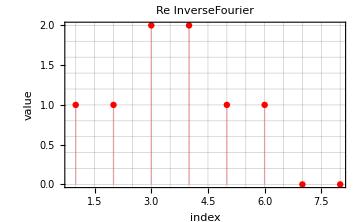

/Users/tomoaki/Library/CloudStorage/Dropbox/code/cpp/builds/build_Fourier/./sample_Re_inv_mathematica.png

```mathematica
len=Length[list];
MyInverseFourier[list_,n_,max_ :(len-1)]:=With[{len=Length[list]},Sum[list[[k+1]]*Exp[I*n*2 π/len*k],{k,0,max}]/len];
Column[inv=InverseFourier[cn,FourierParameters->{-1,-1}],Frame->All]
Column[Table[MyInverseFourier[cn,n]*(Length[list]),{n,0,Length[list]-1,1}],Frame->All]

fig=ListPlot[Re[inv],PlotLabel->"Re InverseFourier",FrameLabel->{"index","value"},Evaluate[plot2Doption]]
Export[FileNameJoin[{NotebookDirectory[],"./sample_Re_inv_"<>casename<>".png"}],fig]
```

```mathematica
(*n-1->-1*)
(*n-2->-2*)
Floor[Length[cn]-1]
shift=If[EvenQ[(Length[cn]-1)/2],{(Length[cn]-1)/2,(Length[cn]-1)/2},{(Length[cn]-1+1)/2,(Length[cn]-1-1)/2}]
Do[Cn[i]=cn[[i+1]],{i,0,shift[[1]]}]
Do[Cn[-i]=cn[[Length[cn]+1-i]],{i,1,shift[[2]]}]
```

7

{4,3}

```mathematica
Column@Table[{i,Re@Cn[i]},{i,-shift[[2]],shift[[1]],1}]
```

{-3,0.176777}
{-2,-2.25833×10^-16}
{-1,-0.176777}
{0,1.}
{1,-0.176777}
{2,-1.72409×10^-17}
{3,0.176777}
{4,0.}

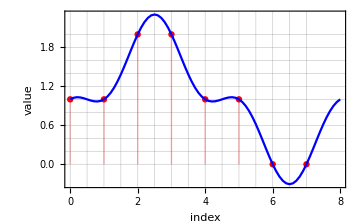

```mathematica
f[t_]:=With[{len=Length[list]},Sum[Cn[n]*Exp[I*n*2 π/len*t],{n,-shift[[2]],shift[[1]],1}]];
fig=Show[
ListPlot[Table[{i-1,list[[i]]},{i,1,Length[list],1}],FrameLabel->{"index","value"},Evaluate[plot2Doption]],
ListPlot[Table[{t,Re[f[t]]},{t,0,Length[list],0.1}],PlotStyle->Blue,Filling->None,Joined->True,Evaluate[plot2Doption]]
,PlotRange->All
]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"./sample_interpolation_"<>casename<>".png"}],fig]
```

/Users/tomoaki/Library/CloudStorage/Dropbox/code/cpp/builds/build_Fourier/./sample_interpolation_mathematica.png

```mathematica
f[t_,expandmax_]:=With[{len=Length[list]},Sum[Cn[n]*Exp[I*n*2 π/len*t],{n,-expandmax,expandmax,1}]];
anim=Manipulate[
Show[
ListPlot[Table[{i-1,list[[i]]},{i,1,Length[list],1}],FrameLabel->{"index","value"},Evaluate[plot2Doption]],
ListPlot[Table[{t,Re[f[t,expandmax]]},{t,0,Length[list],0.1}],PlotStyle->Blue,Filling->None,Joined->True,Evaluate[plot2Doption]]
,PlotRange->All
,PlotLabel->expandmax
],{expandmax,1,Min[shift],1}]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"./sample_convergence_"<>casename<>".gif"}],anim]
```

/Users/tomoaki/Library/CloudStorage/Dropbox/code/cpp/builds/build_Fourier/./sample_convergence_mathematica.gif